# Calcolo risposta al gradino per un sistema LTI-TC che presenta poli multipli

Fdt

```mathematica
G[s_]:=(s-3)/(s^3+6 s^2+9s+4)
```

Calcolo i poli del sistema

```mathematica
Solve[Denominator[G[s]]==0,s]
```

{{s→-4},{s→-1},{s→-1}}

Calcolo la risposta forzata in s

```mathematica
Subscript[Y, f][s_]:=G[s](1/s)
```

```mathematica
Subscript[Y, f][s]
```

(-3+s)/(s (4+9 s+6 s^2+s^3))

```mathematica
Apart[Subscript[Y, f][s]]
```

-3/(4 s)+4/(3 (1+s)^2)+5/(9 (1+s))+7/(36 (4+s))

Scrivo Yf[s]

```mathematica
Subscript[C, 1](1/s)+Subscript[C, 2](1/(s+4))+Subscript[C, 31](1/(s+1))+Subscript[C, 32](1/(s+1)^2)
```

C_1/s+C_2/(4+s)+C_31/(1+s)+C_32/(1+s)^2

```mathematica
Subscript[C, 1]=G[0]
```

-3/4

```mathematica
Subscript[C, 2]=lim_(s->-4) (s+4)Subscript[Y, f][s]
```

7/36

```mathematica
Subscript[C, 32]=lim_(s->-1) (s+1)^2 Subscript[Y, f][s]
```

4/3

```mathematica
Subscript[C, 31]=lim_(s->-1) D[(s+1)^2 Subscript[Y, f][s],s]
```

5/9

```mathematica
InverseLaplaceTransform[Subscript[Y, f][s],s,t]
```

1/36 (-27+7 ⅇ^(-4 t)+4 ⅇ^-t (5+12 t))

```mathematica
Subscript[y, f][t_]:=Subscript[C, 1] UnitStep[t]+Subscript[C, 2] Exp[-4 t]UnitStep[t]+Subscript[C, 31] Exp[-t]UnitStep[t]+Subscript[C, 32] t Exp[-t]UnitStep[t]
```

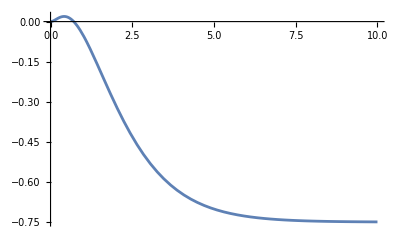

```mathematica
Plot[Subscript[y, f][t],{t,0,10},PlotRange->All]
```